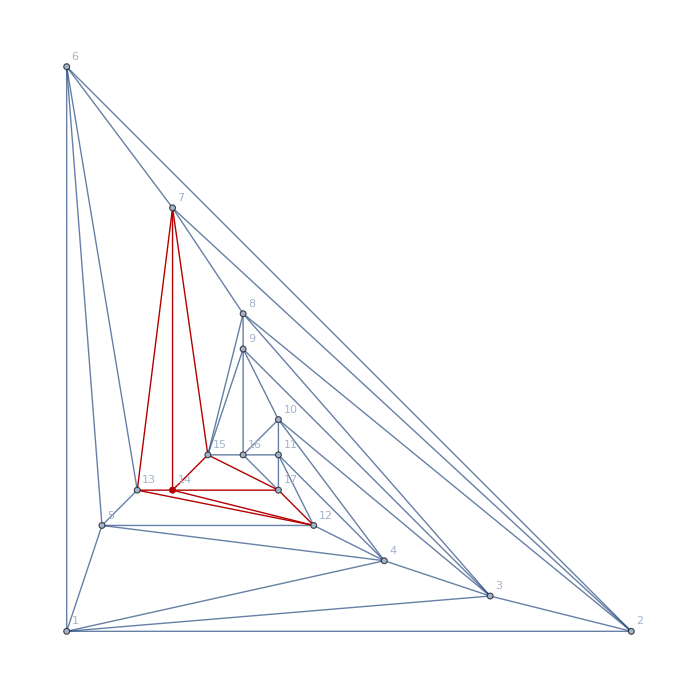

```mathematica
g=Graph[plantri[[8]],GraphHighlight->{7<->13,13<->12,12<->17,17<->15,15<->7,14,7<->14,7<->14,13<->14,12<->14,17<->14,15<->14},GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
ToLogical[g_,max_:4]:=Block[{exp,vertex,vertices,var,var1,var2,edges,edgeIndex,edge},exp=True;
vertices=VertexList[g];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&Element[var,Integers];];
For[vertex=1,vertex≤Length[vertices],vertex++,var=Symbol["x"<>ToString[vertices[[vertex]]]];
exp=exp&&(1≤var≤max);];
edges=EdgeList[g];
For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,edge=edges[[edgeIndex]];
var1=Symbol["x"<>ToString[edge[[1]]]];
var2=Symbol["x"<>ToString[edge[[2]]]];
exp=exp&&var1≠var2;];
exp]
```

```mathematica
exp=ToLogical[g,5]
```

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x6∈Integers&&x7∈Integers&&x8∈Integers&&x9∈Integers&&x10∈Integers&&x11∈Integers&&x12∈Integers&&x13∈Integers&&x14∈Integers&&x15∈Integers&&x16∈Integers&&x17∈Integers&&1≤x1≤5&&1≤x2≤5&&1≤x3≤5&&1≤x4≤5&&1≤x5≤5&&1≤x6≤5&&1≤x7≤5&&1≤x8≤5&&1≤x9≤5&&1≤x10≤5&&1≤x11≤5&&1≤x12≤5&&1≤x13≤5&&1≤x14≤5&&1≤x15≤5&&1≤x16≤5&&1≤x17≤5&&x1≠x2&&x1≠x3&&x1≠x4&&x1≠x5&&x1≠x6&&x2≠x6&&x2≠x7&&x2≠x8&&x2≠x3&&x3≠x8&&x3≠x9&&x3≠x10&&x3≠x4&&x4≠x10&&x4≠x11&&x4≠x12&&x4≠x5&&x5≠x12&&x5≠x13&&x5≠x6&&x6≠x13&&x6≠x7&&x7≠x13&&x7≠x14&&x7≠x15&&x7≠x8&&x8≠x15&&x8≠x9&&x9≠x15&&x9≠x16&&x9≠x10&&x10≠x16&&x10≠x11&&x11≠x16&&x11≠x17&&x11≠x12&&x12≠x17&&x12≠x14&&x12≠x13&&x13≠x14&&x14≠x17&&x14≠x15&&x15≠x17&&x15≠x16&&x16≠x17

```mathematica
36281*120
```

4353720

```mathematica
EdgeCount[g]
```

45

```mathematica
(CompleteBaseCoeff[ ChromaticPolynomial[g,x]]//Rest)
```

{0,0,0,22,36281,1796800,17198421,55339513,78241812,56479726,22766977,5401613,773706,66900,3380,91,1}

```mathematica
N[22*24/694337290,50]
```

7.604373373061959555708148701044127991454988684246×10^-7

```mathematica
Table[StirlingS2[17,k],{k,1,17}]
```

{1,65535,21457825,694337290,5652751651,17505749898,25708104786,20415995028,9528822303,2758334150,512060978,62022324,4910178,249900,7820,136,1}

```mathematica
NullBaseCoeff[ ChromaticPolynomial[g,x]]
```

{0,71265972,-351946840,802461675,-1131475014,1112163274,-812626569,458524982,-204408959,72889503,-20875904,4786421,-868885,122328,-12900,960,-45,1}

```mathematica
ChromaticPolynomial[g,4]
```

528

```mathematica
CompleteBaseCoeff[ ChromaticPolynomial[g2,x]]
```

{ChromaticPolynomial[g2,x]}

```mathematica
528/24
```

22

```mathematica
sols=ToVarsLogical[g,True]
```

$Aborted

```mathematica
Length[sols]
```

528

```mathematica
SolutionToPartition[ol_]:=Block[{assoc=Association[],i,val},
For[i=1,i≤4,i++,
assoc[i]={}
];
For[i=1,i≤Length[ol],i++,
val=ol[[i,2]];
assoc[val]=Append[assoc[val], IntegerString[i,10,2]]
];
Row[Riffle[Sort[Select[Table[StringRiffle[assoc[key],"-"],{key,Keys[assoc]}],#≠""&]],Style["♁",Bold,Red]]]
]
```

```mathematica
SolutionToPartition[ol_,vertices_]:=Block[{assoc=Association[],i,val},
For[i=1,i≤4,i++,
assoc[i]={}
];
Table[val=ol[[i,2]];
assoc[val]=Append[assoc[val], IntegerString[i,10,2]]
,{i,vertices}];
Row[Riffle[Sort[Select[Table[StringRiffle[assoc[key],"-"],{key,Keys[assoc]}],#≠""&]],Style["♁",Bold,Red]]]
]
```

```mathematica
TextForm[2,"00"]
```

TextForm::argx: TextForm called with 2 arguments; 1 argument is expected.

TextForm[2, 00]

```mathematica
SolutionToPartition[{x1->1,x2->2,x3->3,x4->2,x5->3,x6->4,x7->1,x8->4,x9->2,x10->1,x11->3,x12->1,x13->2,x14->4,x15->3,x16->4,x17->2}]
```

01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16

```mathematica
TableForm[Map[SolutionToPartition[#]&,Take[sols,100]]]
```

01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15

```mathematica
ChromaticPolynomial[g,4]
```

528

```mathematica
Map[First,Map[SolutionToPartition[#]&,sols]//Sort//Tally]//Length
```

22

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#]&,sols]//Sort//Tally]]
```

01-07-09-12♁02-05-10-17♁03-11-13-15♁04-06-08-14-16
01-07-09-12♁02-10-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-05-11-15♁06-08-14-16
01-07-10-12♁02-04-09-13-17♁03-06-11-15♁05-08-14-16
01-07-10-12♁02-05-09-17♁03-11-13-15♁04-06-08-14-16
01-07-10-12♁02-09-13-17♁03-05-11-15♁04-06-08-14-16
01-07-10-17♁02-05-09-11-14♁03-06-12-15♁04-08-13-16
01-07-12-16♁02-04-09-13-17♁03-05-11-15♁06-08-10-14
01-07-12-16♁02-04-09-13-17♁03-06-11-15♁05-08-10-14
01-08-10-13-17♁02-04-14-16♁03-06-12-15♁05-07-09-11
01-08-10-13-17♁02-05-09-11-14♁03-06-12-15♁04-07-16
01-08-10-13-17♁02-05-09-11-14♁03-07-12-16♁04-06-15
01-08-10-13-17♁02-05-11-15♁03-07-12-16♁04-06-09-14
01-08-11-14♁02-04-09-13-17♁03-05-07-16♁06-10-12-15
01-08-14-16♁02-04-09-13-17♁03-05-07-11♁06-10-12-15
01-09-11-13♁02-10-12-15♁03-05-07-17♁04-06-08-14-16
01-09-13-17♁02-10-12-15♁03-05-07-11♁04-06-08-14-16
01-10-12-15♁02-04-09-13-17♁03-05-07-11♁06-08-14-16
01-10-12-15♁02-04-09-13-17♁03-05-07-16♁06-08-11-14
01-10-12-15♁02-09-11-13♁03-05-07-17♁04-06-08-14-16
01-10-12-15♁02-09-13-17♁03-05-07-11♁04-06-08-14-16
01-10-13-15♁02-05-09-11-14♁03-07-12-16♁04-06-08-17

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#,{7,15,17,12,13}]&,sols]//Sort//Tally]]
```

07♁15-12♁17-13
07-12♁15♁17-13
07-12♁15-13♁17
07-17♁13♁15-12

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#,Sort[{7,14,15,17,12,13}]]&,sols]//Sort//Tally]]
```

07♁12-15♁13-17♁14
07-12♁13-15♁14♁17
07-12♁13-17♁14♁15
07-17♁12-15♁13♁14

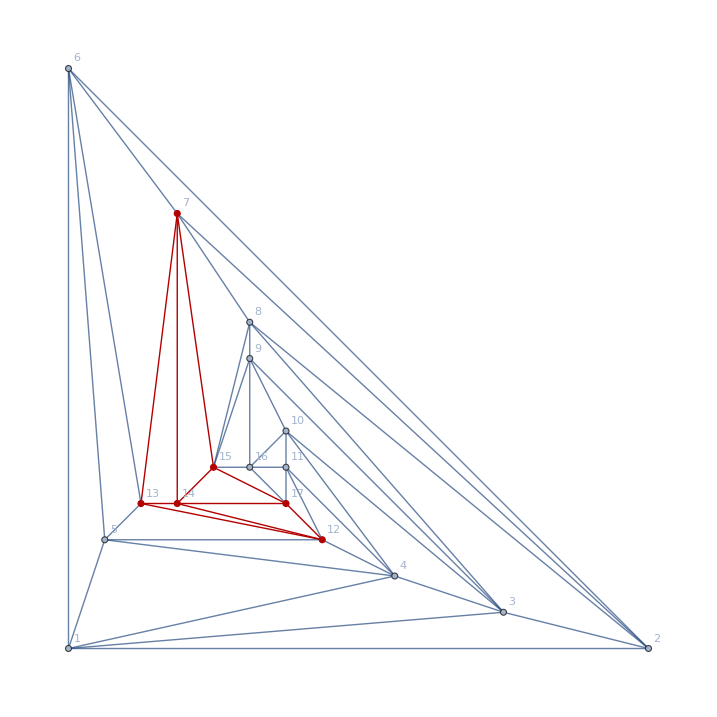

```mathematica
HighlightGraph[Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],NeighborhoodGraph[g,14]]
```

```mathematica
FindPath[g,12,7,{5},All]
```

{{12,13,14,15,8,7},{12,13,14,17,15,7},{12,13,6,2,8,7},{12,13,6,1,2,7},{12,13,5,6,2,7},{12,13,5,1,6,7},{12,13,5,1,2,7},{12,14,15,9,8,7},{12,14,15,8,2,7},{12,14,17,16,15,7},{12,14,17,15,8,7},{12,14,13,6,2,7},{12,14,13,5,6,7},{12,17,16,15,14,7},{12,17,16,15,8,7},{12,17,16,9,15,7},{12,17,16,9,8,7},{12,17,15,14,13,7},{12,17,15,9,8,7},{12,17,15,8,2,7},{12,17,14,15,8,7},{12,17,14,13,6,7},{12,17,11,16,15,7},{12,11,17,16,15,7},{12,11,17,15,14,7},{12,11,17,15,8,7},{12,11,17,14,15,7},{12,11,17,14,13,7},{12,11,16,17,15,7},{12,11,16,17,14,7},{12,11,16,15,14,7},{12,11,16,15,8,7},{12,11,16,9,15,7},{12,11,16,9,8,7},{12,11,10,16,15,7},{12,11,10,9,15,7},{12,11,10,9,8,7},{12,11,10,3,8,7},{12,11,10,3,2,7},{12,11,4,5,6,7},{12,11,4,5,13,7},{12,11,4,3,8,7},{12,11,4,3,2,7},{12,11,4,1,6,7},{12,11,4,1,2,7},{12,5,6,13,14,7},{12,5,6,2,8,7},{12,5,6,1,2,7},{12,5,13,14,15,7},{12,5,13,6,2,7},{12,5,4,3,8,7},{12,5,4,3,2,7},{12,5,4,1,6,7},{12,5,4,1,2,7},{12,5,1,6,13,7},{12,5,1,6,2,7},{12,5,1,3,8,7},{12,5,1,3,2,7},{12,5,1,2,8,7},{12,5,1,2,6,7},{12,4,5,6,13,7},{12,4,5,6,2,7},{12,4,5,13,14,7},{12,4,5,13,6,7},{12,4,5,1,6,7},{12,4,5,1,2,7},{12,4,11,17,15,7},{12,4,11,17,14,7},{12,4,11,16,15,7},{12,4,10,16,15,7},{12,4,10,9,15,7},{12,4,10,9,8,7},{12,4,10,3,8,7},{12,4,10,3,2,7},{12,4,3,9,15,7},{12,4,3,9,8,7},{12,4,3,8,15,7},{12,4,3,8,2,7},{12,4,3,2,8,7},{12,4,3,2,6,7},{12,4,3,1,6,7},{12,4,3,1,2,7},{12,4,1,6,13,7},{12,4,1,6,2,7},{12,4,1,5,6,7},{12,4,1,5,13,7},{12,4,1,3,8,7},{12,4,1,3,2,7},{12,4,1,2,8,7},{12,4,1,2,6,7}}

```mathematica
FindPath[g,12,15,{3},All]
```

{{12,13,14,15},{12,13,7,15},{12,14,17,15},{12,14,7,15},{12,17,16,15},{12,17,14,15},{12,11,17,15},{12,11,16,15}}

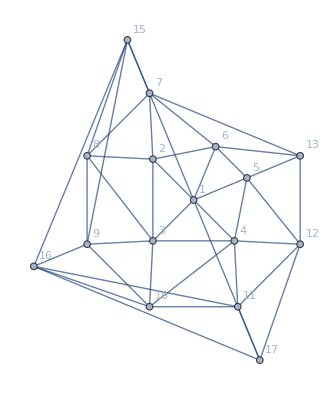

```mathematica
g2=Graph[VertexDelete[g,14],VertexLabels->"Name",GraphLayout->"RadialDrawing"]
```

```mathematica
MobiusMatrix[allGraphs6]
```

{{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,-6,4,4,4,4,4,4,4,4,4,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,24,24,24,24,24,24,-120},202}
 |  |  |  |

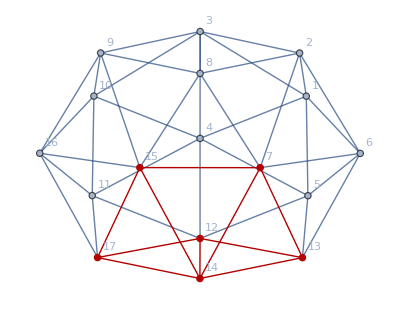

```mathematica
Graph[g,VertexLabels->"Name",GraphLayout->"SpringElectricalEmbedding",GraphHighlight->Join[EdgeList[NeighborhoodGraph[g,14]],VertexList[NeighborhoodGraph[g,14]]]]
```

```mathematica
14
```

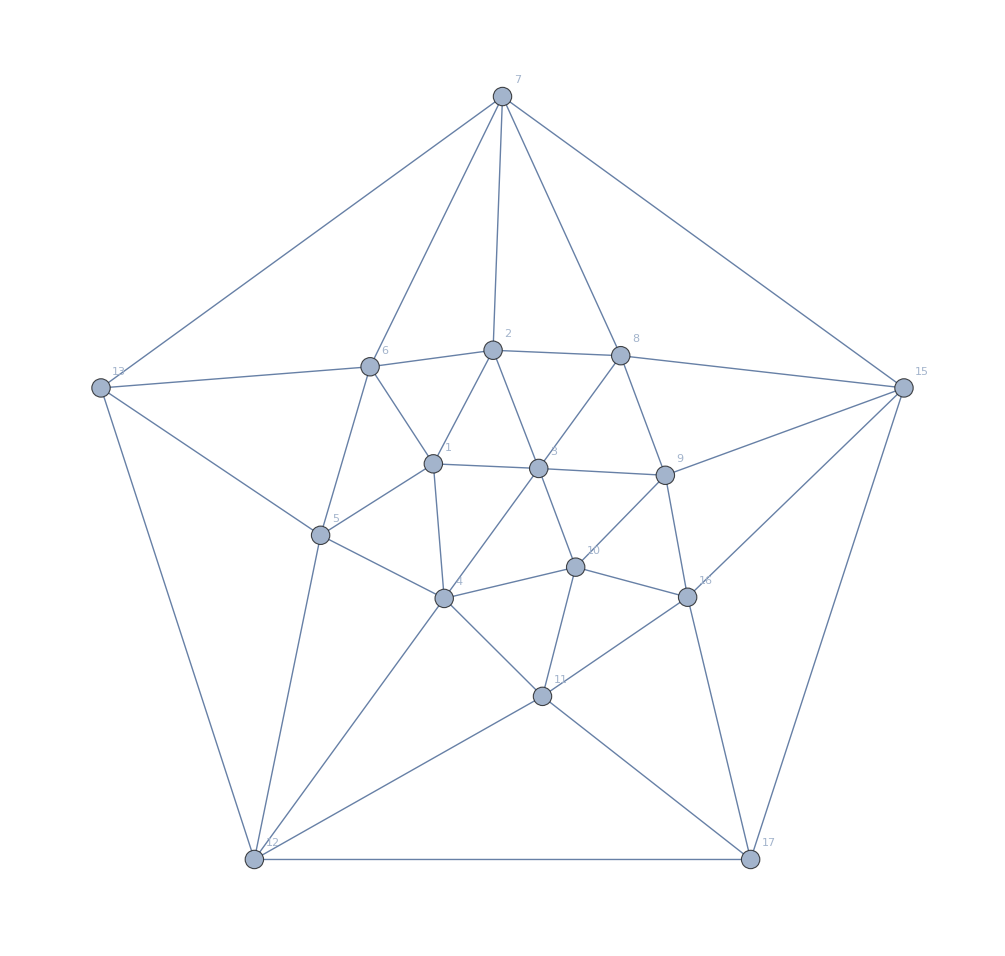

```mathematica
Graph[g2,VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
"01-07-10-12""♁""02-04-09-13-17""♁""03-05-11-15""♁""06-08-14-16"
```

```mathematica
SolutionToPartition2[ol_]:=Block[{assoc=Association[],i,val},
For[i=1,i≤4,i++,
assoc[i]={}
];
For[i=1,i≤Length[ol],i++,
val=ol[[i,2]];
assoc[val]=Append[assoc[val], i]
];
Table[assoc[key],{key,Keys[assoc]}]
]
```

```mathematica
SolutionToPartition2[{x1->1,x2->2,x3->3,x4->2,x5->3,x6->4,x7->1,x8->4,x9->2,x10->1,x11->3,x12->1,x13->2,x14->4,x15->3,x16->4,x17->2}]
```

{{1,7,10,12},{2,4,9,13,17},{3,5,11,15},{6,8,14,16}}

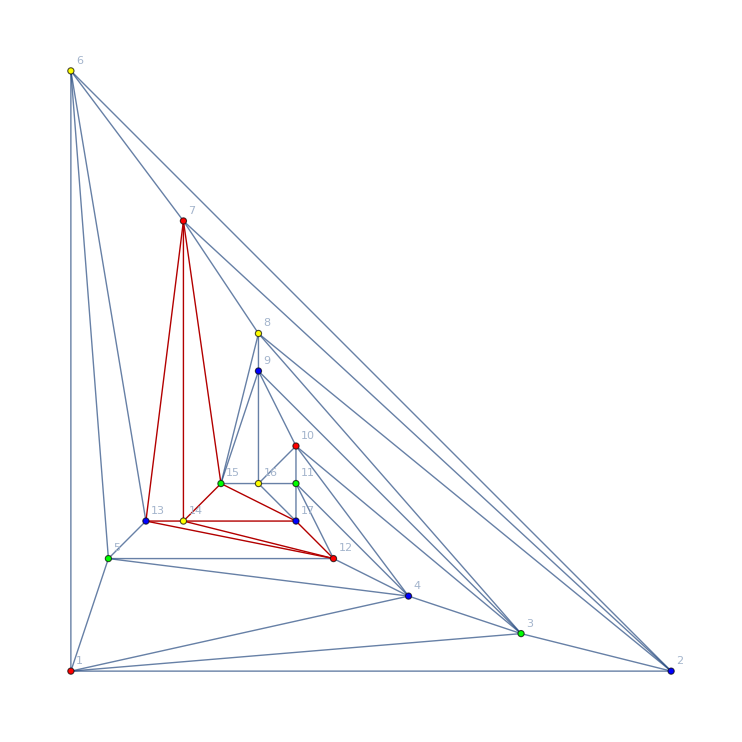

```mathematica
Graph[g,VertexStyle->Join[
Map[#->Red&,{1,7,10,12}],
Map[#->Blue&,{2,4,9,13,17}],
Map[#->Green&,{3,5,11,15}],
Map[#->Yellow&,{6,8,14,16}]
],
VertexLabels->"Name",
GraphHighlight->Join[EdgeList[NeighborhoodGraph[g,14]]],
GraphLayout->"PlanarEmbedding"
]
```

```mathematica
ChromaticPolynomial[g2,4]/24
```

63

```mathematica
sols2=ToVarsLogical[g,True]
```

{{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→1,x10→4,x11→3,x12→1,x13→2,x15→3,x16→2,x17→4},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→1,x10→4,x11→3,x12→4,x13→2,x15→3,x16→2,x17→1},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x15→3,x16→4,x17→2},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→4,x13→2,x15→3,x16→4,x17→1},1505,{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x15→2,x16→1,x17→3},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→4,x10→1,x11→2,x12→1,x13→3,x15→2,x16→3,x17→4},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→4,x10→1,x11→2,x12→4,x13→3,x15→2,x16→3,x17→1}}
 |  |  |  |

```mathematica
SolutionToPartition[{x1->1,x2->2,x3->3,x4->2,x5->3,x6->4,x7->1,x8->4,x9->1,x10->4,x11->3,x12->1,x13->2,x15->3,x16->2,x17->4}]
```

16<|1→{01,07,09,12},2→{02,04,13,15},3→{03,05,11,14},4→{06,08,10,16}|>

01-07-09-12♁02-04-13-15♁03-05-11-14♁06-08-10-16

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#,{7,14,16,12,13},4]&,sols2]//Sort//Tally]]
```

7|EC|GD
7C|E|GD
7C|ED|G
7G|D|EC
7|C|E|GD
7|C|ED|G
7|D|EC|G
7C|D|E|G
7G|C|D|E

```mathematica
TableForm[Map[First,Map[SolutionToPartition[#]&,sols2]//Sort//Tally]]
```

## Embedding and so

```mathematica
Monitor[Table[{k,PlanarGraphQ[EmbedGraphInPlantri8[allGraphs5,k]]},{k,Sort[allGraphs5AtomKeys]}],k]
```

{{29524,False},{29525,False},{29527,False},{29533,False},{29537,True},{29551,False},{29560,False},{29605,False},{29608,False},{29633,False},{29767,False},{29768,True},{29797,False},{29857,True},{29888,True},{30253,False},{30262,True},{30334,False},{30496,True},{30586,True},{31711,False},{31714,False},{31738,False},{31954,False},{31984,False},{32441,True},{32684,True},{36085,False},{36086,False},{36112,False},{36166,False},{36194,False},{36817,False},{36898,False},{38281,False},{38308,False},{39014,True},{49207,False},{49208,True},{49210,False},{49216,True},{49220,True},{49963,True},{49972,True},{51475,False},{51478,False},{52232,True},{56011,True},{56012,True},{56770,True},{58288,True},{59048,True}}

```mathematica
polys=Monitor[Table[{k,ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,k],x]},{k,Sort[allGraphs5AtomKeys]}],k]
```

{{29524,-44638752 x+204166792 x^2-426543264 x^3+545509028 x^4-481367651 x^5+312348303 x^6-154680663 x^7+59730697 x^8-18173424 x^9+4361820 x^10-819388 x^11+118284 x^12-12693 x^13+955 x^14-45 x^15+x^16},{29525,6741180 x-30408108 x^2+62346259 x^3-77791960 x^4+66507803 x^5-41468463 x^6+19538839 x^7-7091889 x^8+1997180 x^9-434804 x^10+72066 x^11-8816 x^12+752 x^13-40 x^14+x^15},{29527,10075668 x-44310800 x^2+88370353 x^3-107092411 x^4+88838370 x^5-53713250 x^6+24533377 x^7-8631800 x^8+2356985 x^9-497838 x^10+80123 x^11-9528 x^12+791 x^13-41 x^14+x^15},{29533,6538392 x-29606880 x^2+60960542 x^3-76395514 x^4+65590832 x^5-41054178 x^6+19406699 x^7-7061956 x^8+1992429 x^9-434297 x^10+72033 x^11-8815 x^12+752 x^13-40 x^14+x^15},{29537,-1242444 x+5513140 x^2-11046467 x^3+13359080 x^4-10959379 x^5+6478241 x^6-2852041 x^7+950278 x^8-240260 x^9+45602 x^10-6321 x^11+606 x^12-36 x^13+x^14},{29551,10477158 x-45811901 x^2+90803005 x^3-109366036 x^4+90205418 x^5-54268793 x^6+24688581 x^7-8661340 x^8+2360662 x^9-498109 x^10+80132 x^11-9528 x^12+791 x^13-41 x^14+x^15},{29560,-2025690 x+8625653 x^2-16533844 x^3+19106804 x^4-14982990 x^5+8477922 x^6-3580571 x^7+1147426 x^8-279749 x^9+51325 x^10-6891 x^11+641 x^12-37 x^13+x^14},{29605,10075668 x-44310800 x^2+88370353 x^3-107092411 x^4+88838370 x^5-53713250 x^6+24533377 x^7-8631800 x^8+2356985 x^9-497838 x^10+80123 x^11-9528 x^12+791 x^13-41 x^14+x^15},{29608,-2997216 x+12457536 x^2-23236766 x^3+26071339 x^4-19815666 x^5+10854453 x^6-4434668 x^7+1374444 x^8-324190 x^9+57590 x^10-7496 x^11+677 x^12-38 x^13+x^14},{29633,-1955220 x+8370368 x^2-16137835 x^3+18758090 x^4-14789593 x^5+8407520 x^6-3563684 x^7+1144844 x^8-279520 x^9+51316 x^10-6891 x^11+641 x^12-37 x^13+x^14},{29767,6741180 x-30408108 x^2+62346259 x^3-77791960 x^4+66507803 x^5-41468463 x^6+19538839 x^7-7091889 x^8+1997180 x^9-434804 x^10+72066 x^11-8816 x^12+752 x^13-40 x^14+x^15},{29768,-1342524 x+5878912 x^2-11620915 x^3+13873979 x^4-11252665 x^5+6589574 x^6-2880642 x^7+955199 x^8-240804 x^9+45637 x^10-6322 x^11+606 x^12-36 x^13+x^14},{29797,-1955220 x+8370368 x^2-16137835 x^3+18758090 x^4-14789593 x^5+8407520 x^6-3563684 x^7+1144844 x^8-279520 x^9+51316 x^10-6891 x^11+641 x^12-37 x^13+x^14},{29857,-1242444 x+5513140 x^2-11046467 x^3+13359080 x^4-10959379 x^5+6478241 x^6-2852041 x^7+950278 x^8-240260 x^9+45602 x^10-6321 x^11+606 x^12-36 x^13+x^14},{29888,339438 x-1435435 x^2+2713956 x^3-3064293 x^4+2319014 x^5-1246929 x^6+490927 x^7-143168 x^8+30786 x^9-4770 x^10+506 x^11-33 x^12+x^13},{30253,6848046 x-30802875 x^2+62976556 x^3-78370811 x^4+66849009 x^5-41604169 x^6+19575914 x^7-7098792 x^8+1998022 x^9-434865 x^10+72068 x^11-8816 x^12+752 x^13-40 x^14+x^15},{30262,-1304094 x+5737579 x^2-11396286 x^3+13668372 x^4-11131440 x^5+6540999 x^6-2867107 x^7+952581 x^8-240464 x^9+45610 x^10-6321 x^11+606 x^12-36 x^13+x^14},{30334,-2032224 x+8650196 x^2-16575496 x^3+19150039 x^4-15013762 x^5+8493558 x^6-3586240 x^7+1148853 x^8-279985 x^9+51348 x^10-6892 x^11+641 x^12-37 x^13+x^14},{30496,-1359264 x+5939176 x^2-11713678 x^3+13954933 x^4-11297126 x^5+6605600 x^6-2884451 x^7+955777 x^8-240855 x^9+45639 x^10-6322 x^11+606 x^12-36 x^13+x^14},{30586,361398 x-1511617 x^2+2825797 x^3-3156295 x^4+2365977 x^5-1262391 x^6+494211 x^7-143601 x^8+30818 x^9-4771 x^10+506 x^11-33 x^12+x^13},{31711,8718090 x-38833829 x^2+78592124 x^3-96778380 x^4+81630015 x^5-50178112 x^6+23280741 x^7-8307623 x^8+2296021 x^9-489699 x^10+79390 x^11-9488 x^12+790 x^13-41 x^14+x^15},{31714,-2544690 x+10782721 x^2-20535628 x^3+23533708 x^4-18258758 x^5+10195043 x^6-4236926 x^7+1332299 x^8-317917 x^9+56968 x^10-7459 x^11+676 x^12-38 x^13+x^14},{31738,-2678520 x+11238478 x^2-21194593 x^3+24071928 x^4-18535034 x^5+10288132 x^6-4257631 x^7+1335244 x^8-318161 x^9+56977 x^10-7459 x^11+676 x^12-38 x^13+x^14},{31954,-1717392 x+7443880 x^2-14555210 x^3+17177591 x^4-13757015 x^5+7941683 x^6-3415017 x^7+1111182 x^8-274209 x^9+50759 x^10-6856 x^11+640 x^12-37 x^13+x^14},{31984,712776 x-2857228 x^2+5091368 x^3-5399010 x^4+3830214 x^5-1929279 x^6+711643 x^7-194566 x^8+39260 x^9-5714 x^10+570 x^11-35 x^12+x^13},{32441,-1164960 x+5215890 x^2-10548671 x^3+12874691 x^4-10653844 x^5+6347031 x^6-2813051 x^7+942343 x^8-239200 x^9+45518 x^10-6318 x^11+606 x^12-36 x^13+x^14},{32684,334872 x-1417260 x^2+2682194 x^3-3032129 x^4+2298224 x^5-1238060 x^6+488438 x^7-142726 x^8+30741 x^9-4768 x^10+506 x^11-33 x^12+x^13},{36085,8718090 x-38833829 x^2+78592124 x^3-96778380 x^4+81630015 x^5-50178112 x^6+23280741 x^7-8307623 x^8+2296021 x^9-489699 x^10+79390 x^11-9488 x^12+790 x^13-41 x^14+x^15},{36086,-1717392 x+7443880 x^2-14555210 x^3+17177591 x^4-13757015 x^5+7941683 x^6-3415017 x^7+1111182 x^8-274209 x^9+50759 x^10-6856 x^11+640 x^12-37 x^13+x^14},{36112,-2678520 x+11238478 x^2-21194593 x^3+24071928 x^4-18535034 x^5+10288132 x^6-4257631 x^7+1335244 x^8-318161 x^9+56977 x^10-7459 x^11+676 x^12-38 x^13+x^14},{36166,-2544690 x+10782721 x^2-20535628 x^3+23533708 x^4-18258758 x^5+10195043 x^6-4236926 x^7+1332299 x^8-317917 x^9+56968 x^10-7459 x^11+676 x^12-38 x^13+x^14},{36194,712776 x-2857228 x^2+5091368 x^3-5399010 x^4+3830214 x^5-1929279 x^6+711643 x^7-194566 x^8+39260 x^9-5714 x^10+570 x^11-35 x^12+x^13},{36817,-1684254 x+7312267 x^2-14329024 x^3+16954837 x^4-13617144 x^5+7882921 x^6-3398219 x^7+1107941 x^8-273803 x^9+50729 x^10-6855 x^11+640 x^12-37 x^13+x^14},{36898,716898 x-2869417 x^2+5105914 x^3-5408225 x^4+3833591 x^5-1929999 x^6+711726 x^7-194570 x^8+39260 x^9-5714 x^10+570 x^11-35 x^12+x^13},{38281,-1418274 x+6271935 x^2-12546723 x^3+15173334 x^4-12455482 x^5+7361649 x^6-3233380 x^7+1071104 x^8-268089 x^9+50142 x^10-6819 x^11+639 x^12-37 x^13+x^14},{38308,632250 x-2561433 x^2+4623222 x^3-4974654 x^4+3584705 x^5-1834138 x^6+686555 x^7-190112 x^8+38750 x^9-5680 x^10+569 x^11-35 x^12+x^13},{39014,262008 x-1149498 x^2+2258001 x^3-2646893 x^4+2074628 x^5-1150961 x^6+465288 x^7-138568 x^8+30257 x^9-4735 x^10+505 x^11-33 x^12+x^13},{49207,6848046 x-30802875 x^2+62976556 x^3-78370811 x^4+66849009 x^5-41604169 x^6+19575914 x^7-7098792 x^8+1998022 x^9-434865 x^10+72068 x^11-8816 x^12+752 x^13-40 x^14+x^15},{49208,-1359264 x+5939176 x^2-11713678 x^3+13954933 x^4-11297126 x^5+6605600 x^6-2884451 x^7+955777 x^8-240855 x^9+45639 x^10-6322 x^11+606 x^12-36 x^13+x^14},{49210,-2032224 x+8650196 x^2-16575496 x^3+19150039 x^4-15013762 x^5+8493558 x^6-3586240 x^7+1148853 x^8-279985 x^9+51348 x^10-6892 x^11+641 x^12-37 x^13+x^14},{49216,-1304094 x+5737579 x^2-11396286 x^3+13668372 x^4-11131440 x^5+6540999 x^6-2867107 x^7+952581 x^8-240464 x^9+45610 x^10-6321 x^11+606 x^12-36 x^13+x^14},{49220,361398 x-1511617 x^2+2825797 x^3-3156295 x^4+2365977 x^5-1262391 x^6+494211 x^7-143601 x^8+30818 x^9-4771 x^10+506 x^11-33 x^12+x^13},{49963,-1359534 x+5940931 x^2-11718142 x^3+13961000 x^4-11302086 x^5+6608164 x^6-2885297 x^7+955950 x^8-240875 x^9+45640 x^10-6322 x^11+606 x^12-36 x^13+x^14},{49972,374628 x-1556626 x^2+2890120 x^3-3207284 x^4+2390680 x^5-1269922 x^6+495628 x^7-143752 x^8+30825 x^9-4771 x^10+506 x^11-33 x^12+x^13},{51475,-1684254 x+7312267 x^2-14329024 x^3+16954837 x^4-13617144 x^5+7882921 x^6-3398219 x^7+1107941 x^8-273803 x^9+50729 x^10-6855 x^11+640 x^12-37 x^13+x^14},{51478,716898 x-2869417 x^2+5105914 x^3-5408225 x^4+3833591 x^5-1929999 x^6+711726 x^7-194570 x^8+39260 x^9-5714 x^10+570 x^11-35 x^12+x^13},{52232,322452 x-1373466 x^2+2616548 x^3-2976688 x^4+2268955 x^5-1227989 x^6+486168 x^7-142401 x^8+30714 x^9-4767 x^10+506 x^11-33 x^12+x^13},{56011,-1164960 x+5215890 x^2-10548671 x^3+12874691 x^4-10653844 x^5+6347031 x^6-2813051 x^7+942343 x^8-239200 x^9+45518 x^10-6318 x^11+606 x^12-36 x^13+x^14},{56012,334872 x-1417260 x^2+2682194 x^3-3032129 x^4+2298224 x^5-1238060 x^6+488438 x^7-142726 x^8+30741 x^9-4768 x^10+506 x^11-33 x^12+x^13},{56770,322452 x-1373466 x^2+2616548 x^3-2976688 x^4+2268955 x^5-1227989 x^6+486168 x^7-142401 x^8+30714 x^9-4767 x^10+506 x^11-33 x^12+x^13},{58288,262008 x-1149498 x^2+2258001 x^3-2646893 x^4+2074628 x^5-1150961 x^6+465288 x^7-138568 x^8+30257 x^9-4735 x^10+505 x^11-33 x^12+x^13},{59048,-87336 x+354054 x^2-634649 x^3+670748 x^4-467960 x^5+227667 x^6-79207 x^7+19787 x^8-3490 x^9+415 x^10-30 x^11+x^12}}

```mathematica
Table[{k[[1]],k[[2]]/.x->4},{k,polys}]
```

{{29524,0},{29525,240},{29527,144},{29533,480},{29537,336},{29551,264},{29560,744},{29605,144},{29608,0},{29633,240},{29767,240},{29768,336},{29797,240},{29857,336},{29888,264},{30253,264},{30262,696},{30334,192},{30496,384},{30586,264},{31711,216},{31714,72},{31738,192},{31954,192},{31984,96},{32441,480},{32684,288},{36085,216},{36086,192},{36112,192},{36166,72},{36194,96},{36817,312},{36898,120},{38281,168},{38308,216},{39014,384},{49207,264},{49208,384},{49210,192},{49216,696},{49220,264},{49963,504},{49972,624},{51475,312},{51478,120},{52232,432},{56011,480},{56012,288},{56770,432},{58288,384},{59048,384}}

```mathematica
allGraphs5[29608,"graph"]
```

-Graphics-

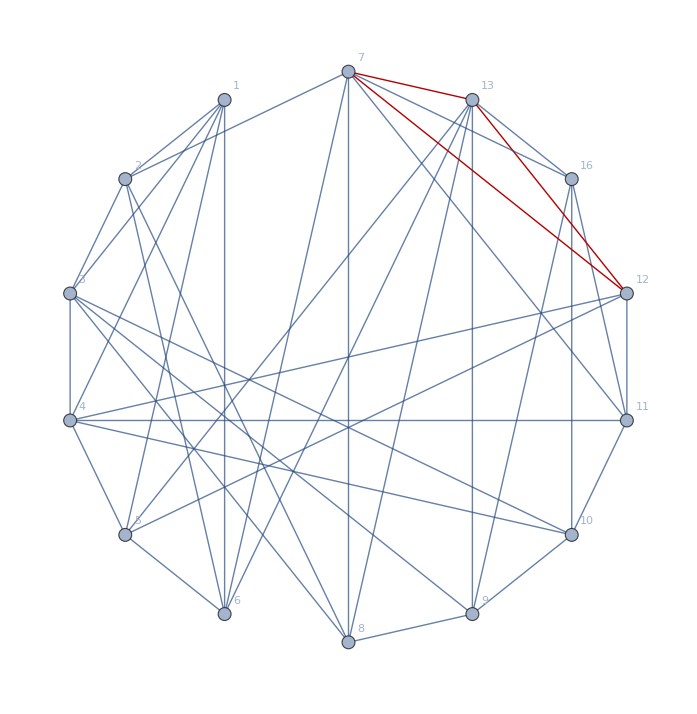

```mathematica
int=Graph[EmbedGraphInPlantri8[allGraphs5,29608],VertexLabels->"Name" ,GraphHighlight->{7<->13,13<->12,12<->7},VertexLabels->"Name",GraphLayout->"CircularEmbedding"]
```

```mathematica
PlanarGraphQ[int]
```

False

```mathematica
FindClique[int,5]
```

{{6,13,7}}

```mathematica
SolsFourStrict[g_,count_:4]:=Block[{sols,four},
sols=FindFullFormula[g];
four=Select[sols,StringCount[SymbolName[#],"x"]==count-1&];
Map[SymbolToLabel2[#,VertexCount[g]]&, Sort[four]]
]
```

```mathematica
intform=FindFullFormula[int];
```

```mathematica
Take[intform,5]
```

{v1x2x3x4x5x6x7x8x9xaxbxcxdxg,v1x2x3x4x5x6x7x8x9xaxbxcgxd,v1x2x3x4x5x6x7x8x9xaxbdxcxg,v1x2x3x4x5x6x7x8x9xaxbdxcg,v1x2x3x4x5x6x7ax8x9xbxcxdxg}

```mathematica
Select[intform,StringCount[SymbolName[#],"x"]==3&]
```

{}

```mathematica
VertexList[int]//Sort
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,16}

## Double diagonal graphs

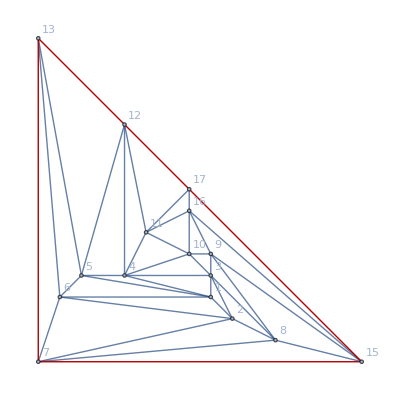

```mathematica
naked=VertexDelete[Graph[plantri[[8]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding", GraphHighlight->{7<->13,13<->12,12<->17,17<->15,15<->7}],14]
```

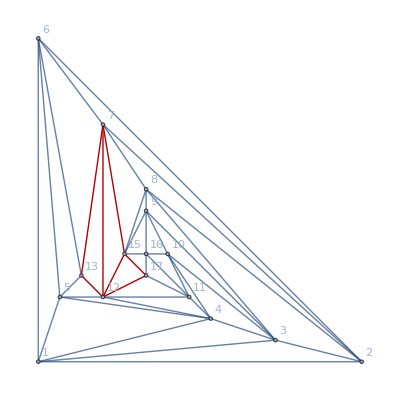

```mathematica
gr1=Graph[EdgeAdd[naked,{12<->7,12<->15}],GraphHighlight->{12<->7,12<->15}]
```

```mathematica
PlanarGraphQ[gr1]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr1,12<->7]]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr1,12<->15]]
```

True

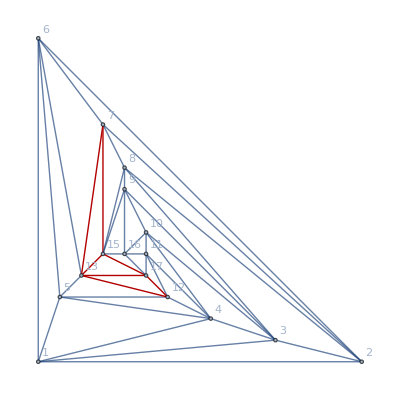

```mathematica
gr2=Graph[EdgeAdd[naked,{13<->17,13<->15}],GraphHighlight->{13<->17,13<->15}]
```

```mathematica
PlanarGraphQ[gr2]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr1,13<->17]]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr1,13<->15]]
```

True

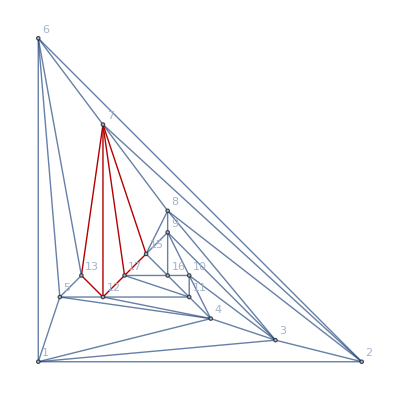

```mathematica
gr3=Graph[EdgeAdd[naked,{7<->17,7<->12}],GraphHighlight->{7<->17,7<->12}]
```

```mathematica
PlanarGraphQ[gr3]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr3,7<->17]]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr3,7<->12]]
```

True

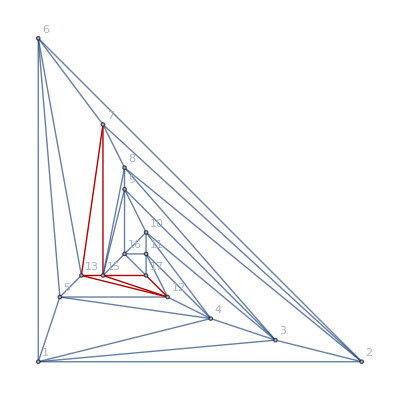

```mathematica
gr4=Graph[EdgeAdd[naked,{15<->12,15<->13}],GraphHighlight->{15<->12,15<->13}]
```

```mathematica
PlanarGraphQ[EdgeContract[gr4,15<->12]]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr4,15<->13]]
```

True

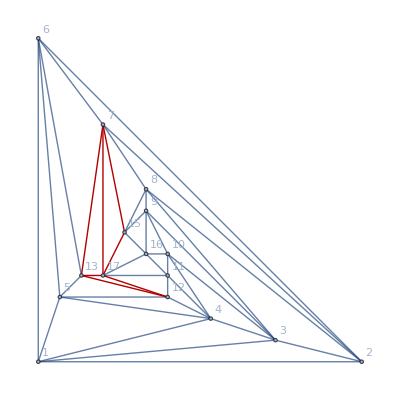

```mathematica
gr5=Graph[EdgeAdd[naked,{17<->13,17<->7}],GraphHighlight->{17<->13,17<->7}]
```

```mathematica
PlanarGraphQ[EdgeContract[gr5,17<->13]]
```

True

```mathematica
PlanarGraphQ[EdgeContract[gr5,17<->7]]
```

True

```mathematica
SolsFourStrict[gr1,4]
```

$Aborted

```mathematica
{1,{2,4},{3,5}}
```

```mathematica
{12,{13,15},{7,17}}
```

```mathematica
boega=Graph[EdgeAdd[naked,{13<->15,7<->17}],GraphHighlight->{13<->15,7<->17}]
```

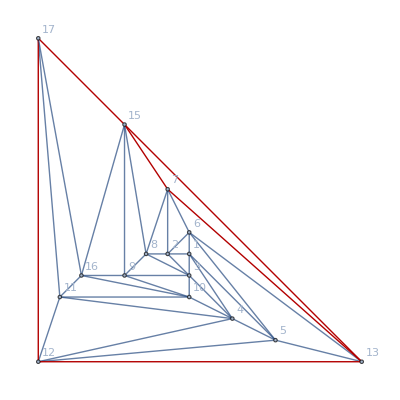

```mathematica
boega2=Graph[EdgeAdd[naked,{13<->15}],GraphHighlight->{13<->15}]
```

```mathematica
PlanarGraphQ[boega]
```

False

```mathematica
FindClique[boega]
```

{{1,2,3}}

```mathematica
FindGraphInSet
```

```mathematica
FindFullFormula2[g_]:=Block[{},
FindFullFormula2[g,Table[{v},{v,VertexList[g]}]]
]
```

```mathematica
FindFullFormula2[gstart_,vstart_]:=Block[{edge,pos1,pos2,v2,result={}, stack={},g,v,hits=0},
stack= {{gstart,vstart}};
Monitor[
While[stack≠{},
{g,v}=First[stack];
stack=Rest[stack];
If[CompleteGraphQ[g],
hits++;
If[VertexCount[g]==4,
result=Append[result,SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]]
]
,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
stack=Append[stack,{VertexContract[g,{edge[[1]],edge[[2]]}],v2}];
stack=Append[stack,{EdgeAdd[g,edge],v}]
];
],
{Length[stack],Length[result],hits,VertexCount[g],EdgeCount[g]}
];
result
]
```

```mathematica
allGraphs5[2,"graph"]
```

-Graphics-

```mathematica
FindFullFormula2[allGraphs6[0,"graph"]]
```

{v12x34x5x6,v12x35x4x6,v12x36x4x5,v123x4x5x6,v13x24x5x6,v13x25x4x6,v13x26x4x5,v14x25x3x6,v14x26x3x5,v15x26x3x4,v12x3x45x6,v12x3x46x5,v124x3x5x6,v13x2x45x6,v13x2x46x5,v134x2x5x6,v14x23x5x6,v14x2x35x6,v14x2x36x5,v15x23x4x6,v15x24x3x6,v15x2x36x4,v16x23x4x5,v16x24x3x5,v16x25x3x4,v12x3x4x56,v125x3x4x6,v13x2x4x56,v135x2x4x6,v14x2x3x56,v145x2x3x6,v15x2x34x6,v15x2x3x46,v16x2x34x5,v16x2x35x4,v1x23x45x6,v1x23x46x5,v1x234x5x6,v1x24x35x6,v1x24x36x5,v1x25x36x4,v126x3x4x5,v136x2x4x5,v146x2x3x5,v156x2x3x4,v16x2x3x45,v1x23x4x56,v1x235x4x6,v1x24x3x56,v1x245x3x6,v1x25x34x6,v1x25x3x46,v1x26x34x5,v1x26x35x4,v1x236x4x5,v1x246x3x5,v1x256x3x4,v1x26x3x45,v1x2x34x56,v1x2x345x6,v1x2x35x46,v1x2x346x5,v1x2x356x4,v1x2x36x45,v1x2x3x456}

```mathematica
Length[solsNaked]
```

```mathematica
ChromaticPolynomial[naked,4]
```

1512

```mathematica
Table[(ChromaticPolynomial[naked,k]/k!),{k,4,VertexCount[naked]}]
```

{63,31429,1876613/2,13547961/2,476701579/24,3705902993/120,2384250921/80,14227188529/720,389129016023/40320,147213813301/40320,575851302139/518400,11166684461699/39916800,1058440998809/17740800}

```mathematica
Sum[(ChromaticPolynomial[naked,k]/k!),{k,4,4}]
```

63

```mathematica
63*24
```

```mathematica
solsG=FindFullFormula2[g]
```

```mathematica
solsNaked=FindFullFormula2[naked]
```

$Aborted

```mathematica
FactorInteger[1739210822418655776]
```

{{2,5},{3,1},{1540541,1},{11760011191,1}}

```mathematica
FindFullFormula2[Graph[plantri[[1]]]]
```

{v179x24bx35cx68a,v179x25cx36ax48b,v17ax259x36cx48b,v18ax24bx36cx579,v19bx24cx357x68a,v17ax29bx35cx468,v18bx24cx36ax579,v18ax29bx357x46c,v18bx259x37ax46c,v19bx25cx37ax468}

```mathematica
naked//VertexCount
```

16

```mathematica
FindFullFormula2[naked]
```